```mathematica
<<BISfit`;
<<Data`;
Needs["PlotLegends`"];
```

```mathematica
Clear["@"];
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear :: wrsym will be suppressed during this calculation.

```mathematica
(* check new nxr data, *)
```

```mathematica
data=nxrData[];
(*fd=Filterd[data[[9]]];*)
(*fdata=Map[Filterd,data];*)
(*fdata[[All,All,1]];*)
```

```mathematica
Dimensions[data]
```

{50,2,138,2}

```mathematica
ffdata=Flatten[data,{{1},{2},{3,4}}];
(*Dimensions[ffdata]
sdata=Standardize[ffdata];
nsdata=Reap[For[i=1;td=sdata,i≤Length[data],i++,
Sow[Take[td,2]];
td=Drop[td,2];
]][[2,1]];
Dimensions[nsdata]*)
fdata=ffdata;
Dimensions[fdata]
```

{50,2,276}

```mathematica
(* first use not normalized data*)
```

```mathematica
(*first filter bad data. NO need here*)
```

```mathematica
(*fdata=Map[Filterd,data];
Dimensions[fdata]*)
```

```mathematica
(* Euclidean distance distribution*)
```

```mathematica
ddiff=Flatten[Reap[For[i=1,i≤Length[fdata]-1,i++,
For[j=i+1,j≤Length[fdata],j++,
Sow[Flatten[Outer[EuclideanDistance,fdata[[i]],fdata[[j]],1]]]
]]
][[2,1]]];

dsame=Reap[For[i=1,i≤Length[fdata],i++,
For[j=1,j≤Length[fdata[[i]]]-1,j++,
For[k=j+1,k<=Length[fdata[[i]]],k++,
Sow[EuclideanDistance[fdata[[i]][[j]],fdata[[i]][[k]]]];
(*Sow[-Mdistance[fdata[[i]][[j]],fdata[[i]][[k]]]];*)
]]]
][[2,1]];
```

```mathematica
{ns,nd}={Length[dsame],Length[ddiff]}
```

{50,4900}

```mathematica
Min[dsame]
Max[dsame]
Min[ddiff]
Max[ddiff]
```

206.842

24353.4

426.974

29323.7

```mathematica
hs=Histogram[dsame,{0,70000,200},"Probability",ColorFunction->Function[{x},Black]];
hd=Histogram[ddiff,{0,70000,400},"Probability",ChartStyle->Opacity[0.5](*,ColorFunction->Function[{x},Black]*)];
```

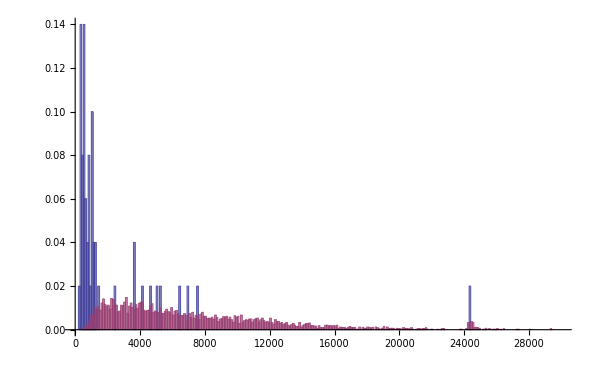

```mathematica
Histogram[{dsame,ddiff},{0,30000,100},"Probability",ChartLayout->"Overlapped"]
```

```mathematica
Show[hs,hd,PlotRange->{{0,20000},{0,0.2}},FrameLabel->{"Frequency (Hz)","Resistance (Ω)"}]
```

-Graphics-

```mathematica
dx=200;
dds=BinCounts[dsame,{0,30000,dx}]/ns;
ddd=BinCounts[ddiff,{0,30000,dx}]/nd;
```

```mathematica
dist=Table[i*dx,{i,0,Length[ddd]-1}];
pdds=Transpose[{dist,dds}];
pddd=Transpose[{dist,ddd}];
```

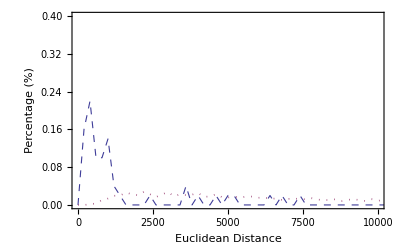

```mathematica
ListPlot[{pdds,pddd},Joined->True,PlotRange->{{0,10000},{0,0.4}},Frame->True,FrameLabel->{"Euclidean Distance","Percentage (%)"},PlotStyle->{{Dashed,Thickness[0.002]},{Dotted,Thickness[0.003]}},PlotLegend->{"Innerclass", "Interclass"},LegendShadow->None]
```

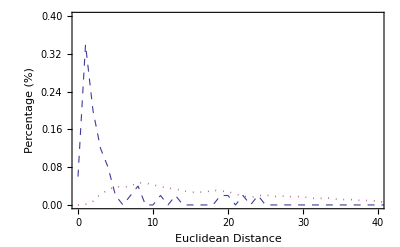

```mathematica
(* now try normalize the data first*)
```

```mathematica
ffdata=Flatten[fdata,1];
Dimensions[ffdata]
sdata=Standardize[ffdata];
nsdata=Reap[For[i=1;td=sdata,i≤Length[fdata],i++,
Sow[Take[td,2]];
td=Drop[td,2];
]][[2,1]];

Dimensions[nsdata]
```

{100,276}

{50,2,276}

{100,276}

{50,2,276}

```mathematica
ddiff=Flatten[Reap[For[i=1,i≤Length[nsdata]-1,i++,
For[j=i+1,j≤Length[nsdata],j++,
Sow[Flatten[Outer[EuclideanDistance,nsdata[[i]],nsdata[[j]],1]]]
]]
][[2,1]]];

dsame=Reap[For[i=1,i≤Length[nsdata],i++,
For[j=1,j≤Length[nsdata[[i]]]-1,j++,
For[k=j+1,k<=Length[nsdata[[i]]],k++,
Sow[EuclideanDistance[nsdata[[i]][[j]],nsdata[[i]][[k]]]];
(*Sow[-Mdistance[fdata[[i]][[j]],fdata[[i]][[k]]]];*)
]]]
][[2,1]];
```

```mathematica
Min[dsame]
Max[dsame]
Min[ddiff]
Max[ddiff]
```

0.717151

24.2332

1.52115

74.5894

```mathematica
Length[dsame]
```

50

```mathematica
Histogram[{dsame,ddiff},{0,12,0.1},"Probability",ChartLayout->"Overlapped"];
```

```mathematica
dds=BinCounts[dsame,{0,60,1}]/ns;
ddd=BinCounts[ddiff,{0,60,1}]/nd;
```

```mathematica
ListPlot[{dds,ddd},Joined->True,PlotRange->{{0,60},{0,0.4}},Frame->True,FrameLabel->{"Euclidean Distance","Percentage (%)"},PlotStyle->{{Dashed,Thickness[0.002]},{Dotted,Thickness[0.003]}},PlotLegend->{"Innerclass", "Interclass"},LegendShadow->None]
```

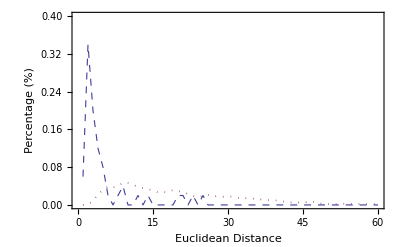

```mathematica
(* try student test in NXR_eucDist_TTEst.nb*)
```